# Experiment with drawing pictures for REED.tex on betweenness

```mathematica
dir=SetDirectory[NotebookDirectory[]];
NotebookEvaluate[dir<>"/lib/pow-reed.nb"]
```

title=Princess of Wales Hospital blood glucometer case
      authors=Harold Thimbleby
      version=v3
      date=10 September 2025
      and: communities, edges, groups, highlights, keywords, notes, vertexNames

Replicate  edges x -> y if x or y in groups

```mathematica
nameExpand=Map[("name"->"nodes")/.#&,groups];expandRule[u_->v_]:=Module[{ul=u/.nameExpand,vl=v/.nameExpand},
Outer[Rule,If[Head[ul]===List,ul,{ul}],If[Head[vl]===List,vl,{vl}]]
]
expandedEdges=Flatten@Map[expandRule,edges];
```

```mathematica
g=Graph@expandedEdges;
```

```mathematica
nameExpand
```

{xceedpro→{18,17,16},hospital→{unknowndatabaselogs,unknownEdits,networks,backups,9,8,7,6unknown,6,5,4,10}}

```mathematica
"hospital"/.nameExpand
```

{unknowndatabaselogs,unknownEdits,networks,backups,9,8,7,6unknown,6,5,4,10}

```mathematica
vlist=VertexList[expandedEdges];
```

```mathematica
xb={11.,22.5,77.5,0.,16.,1.5,17.,0.,11.,14.5,18.,16.,0.,0.,14.,0.,0.,0.,0.,0.,0.}
```

{11.,22.5,77.5,0.,16.,1.5,17.,0.,11.,14.5,18.,16.,0.,0.,14.,0.,0.,0.,0.,0.,0.}

```mathematica
Rescale[xb^.9]+.1
```

{0.272537,0.428543,1.1,0.1,0.341733,0.128715,0.355289,0.1,0.272537,0.321238,0.368766,0.341733,0.1,0.1,0.31436,0.1,0.1,0.1,0.1,0.1,0.1}

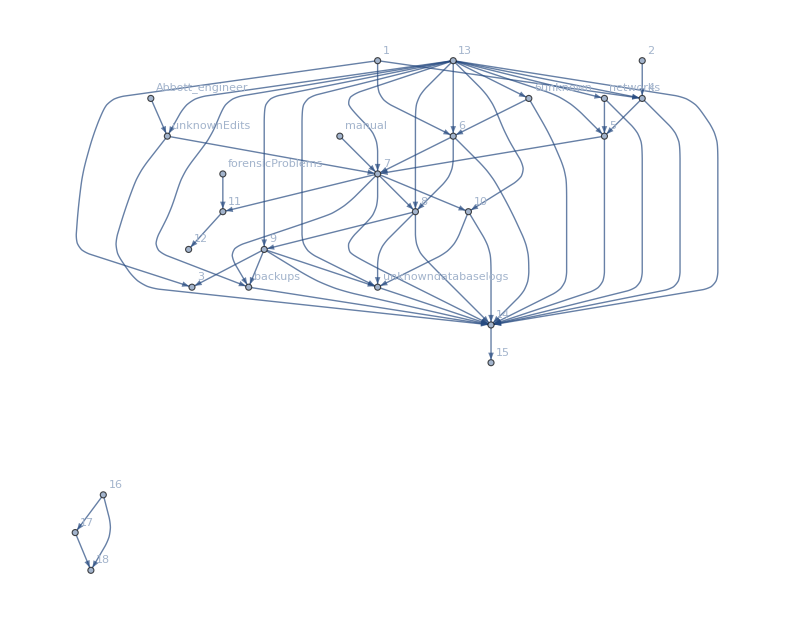

```mathematica
Graph[g,VertexLabels-> All]
```

23 {0.1,0.443056,2.,0.1,0.548611,0.838889,0.1,0.1,0.1,0.390278,0.575,0.8125,0.443056,0.205556,0.1,0.1,0.469444,0.1,0.1,0.1,0.1,0.1,0.1}

3 {3.,3.,3.}

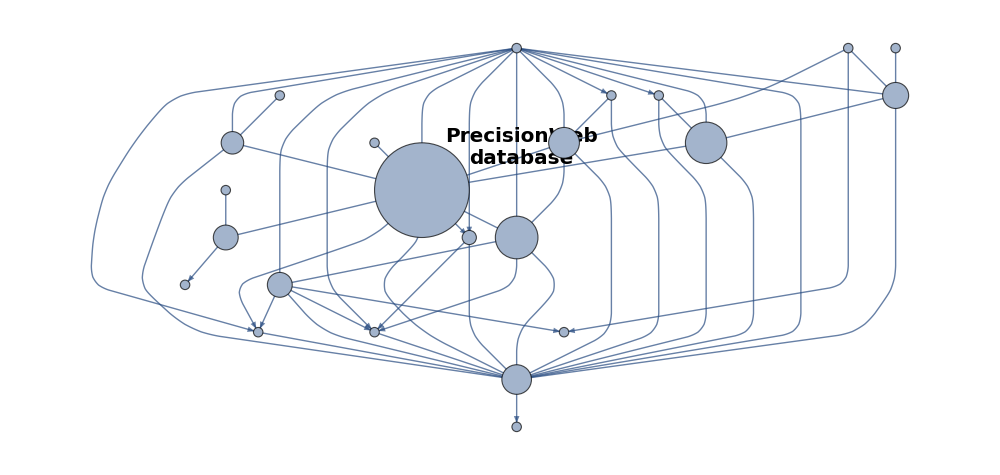
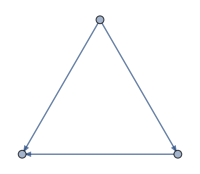

```mathematica
bg=Map[Module[{b,g},
b=BetweennessCentrality[g=Subgraph[expandedEdges,#]];
Print[Length[b]," ",Rescale[Rescale[b],{0,1},{If[Length@b==3,3,.1],2}]];
HighlightGraph[g,Map[Style[#,Darker[Red]]&,VertexList[g]],VertexSize-> Thread[VertexList[g]-> Rescale[Rescale[b],{0,1},{If[Length@b==3,.05,.2],2}]],
(VertexLabels->{"7"->Placed[Style["PrecisionWeb\ndatabase",20,Bold,Black],{1.55,.95}]})
]]&,WeaklyConnectedComponents[expandedEdges]];
betweennessplot=Show[{Show[bg[[1]],ImageSize->1000],Show[bg[[2]],ImageSize->50]}];
betweennessplot=Row[{Show[bg[[1]],ImageSize->1000],Show[bg[[2]],ImageSize->200]}]
```

```mathematica
Export["../REED-paper/figures/betweenness.png",betweennessplot]
```

../REED-paper/figures/betweenness.png

```mathematica
Row[{Show[bg[[1]],ImageSize->1000],Show[bg[[2]],ImageSize->100]}]
```

-Graphics--Graphics-

## Now try and infer relations between highlights and keyword

A keyword implies a color if all nodes with that keyword have that color
A color implies a keyword if all nodes with that color have that keyword
A color and keyword are equivalent if the color implies the keyword and the keyword implies the color

```mathematica
allnodes=Union@Flatten[edges/.Rule->List]
```

```mathematica
allhighlights=Union[highlights/.(_->color_)->color]
```

```mathematica
allkeywords=Union@Flatten[Union[keywords/.(_->keyword_)->keyword]]
```

```mathematica
generalisedKeywords=Append[keywords,_->{}]
```

```mathematica
highlightof[node_]:=node/.highlights;
keywordsof[node_]:=node/.generalisedKeywords;
highlightednodes[color_]:=Cases[{#,highlightof@#}&/@allnodes,{node_,color}->node];
keywordednodes[keyword_]:=DeleteCases[Map[Module[{},
If[MemberQ[keywordsof[#],keyword],#,{}]
]&,allnodes],{}]
highlightof/@keywordednodes["Audit"]
```

```mathematica
highlightednodes["yellow"]
```

Find intersection of keywords for all nodes of highlight h

```mathematica
highlightof/@allnodes
```

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@Map[keywordsof,highlightednodes[#]]]&,allhighlights],Implies[_,{}]]
```

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@List/@Map[highlightof,keywordednodes[#]]]&,allkeywords],Implies[_,{}]]
```

```mathematica
keywordednodes["Corruption of evidence"]
```

```mathematica
{"Abbott_engineer"}
```

```mathematica
keywordsof/@%
```

```mathematica
keywordednodes["PrecisionWeb database"]
```

```mathematica
Print["=end-"]
```

```mathematica
HighlightGraph[,vlist,VertexSize->Thread[vlist->Rescale[b]]]
```

```mathematica
g=ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
clique=FindClique[g];
plot=HighlightGraph[g, Subgraph[g,clique]];
Export["plot.pdf",plot]
```